# Quantum error correction essentials.

## For old versions of Mathematica, include the following.

```mathematica
(*Needs["PlotLegends`"]*)
```

## Preprocessing for an error correcting code.

### Remember to make the following changes depending on the context. 1. path: set to the full path of the HardwareEfficient folder. 2. codename: set to the name of the code. Predefined names are: “Cat”, “FiveQubit”, “Steane”. To define new codes: 1. Create a new folder in codedata/ with the name of the code. 2. Create 4 text files. One with the name of the code and its N, K and D. The other three should contain the Pauli basis 3. Run the Python code in qcode.py as: python qcode.py <name of the code> 4. Run the Python code in qport.py as: python qcode.py <name of the code> 3. nqubits: number of physical qubits in the QECC. 4. kqubits: number of logical qubits in the QECC.

```mathematica
path = "/Users/pavithran/Documents/LDPC/Channel_Flow/chflow/analytics";
codename = "Steane";
nqubits = 7;kqubits = 1;
```

```mathematica
LogicalAction={IntegerPart[Import[StringJoin[path,"/data/",codename,"/",codename,"_LA_I.txt"],"Table"]],IntegerPart[Import[StringJoin[path,"/data/",codename,"/",codename,"_LA_X.txt"],"Table"]],IntegerPart[Import[StringJoin[path,"/data/",codename,"/",codename,"_LA_Y.txt"],"Table"]],IntegerPart[Import[StringJoin[path,"/data/",codename,"/",codename,"_LA_Z.txt"],"Table"]]};
Phases=IntegerPart[Import[StringJoin[path,"/data/",codename,"/",codename,"_realPhases.txt"],"Table"]];
StabilizerSyndromeSigns = IntegerPart[Import[StringJoin[path,"/data/",codename,"/",codename,"_SS.txt"],"Table"]];
lookup = Flatten[IntegerPart[Import[StringJoin[path,"/data/",codename,"/",codename,"_syndLookUp.txt"],"Table"]]];
Algebra[i_,j_]:=If[i==0||j==0||i==j,1,-1];
```

# Generalized Amplitude damping channel

## Noise characterization

### Process matrix (Γ). Γ_ij==Tr[ℰ (P_i) P_j] where P_i is the i^th Pauli matrix. Γ = (1 | 0 | 0 | λ 0 | (1-2 p) √(1-λ) | 0 | 0 0 | 0 | (1-2 p) √(1-λ) | 0 0 | 0 | 0 | 1-λ)

```mathematica
process[p_,λ_]:=Refine[{{1,0,0,λ},{0,(1-2*p)*Sqrt[1-λ],0,0},{0,0,(1-2*p)*Sqrt[1-λ],0},{0,0,0,1-λ}},Element[p,Reals]&&Element[λ,Reals]&&0≤p≤1&&0≤λ≤1];
```

## Noise strength measures

### Entanglement infidelity = 1 - (Tr(Γ))/4.

```mathematica
Infidelity[Γ_]:=Re[1 - Tr[Γ]/4];
infid [p_,λ_]:=Infidelity[process[p,λ]];
```

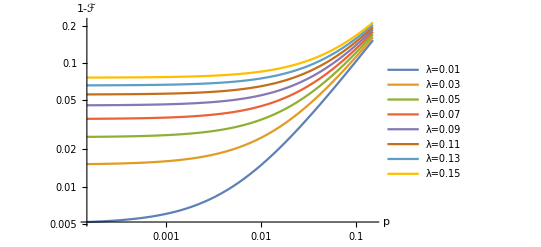

```mathematica
range=Table[λ,{λ,0.01,0.15,0.02}];LogLogPlot[Evaluate[Table[Refine[infid[p,λ],Element[p,Reals]&&Element[λ,Reals]&&0≤p≤1&&0≤λ≤1],{λ,range}]],{p,0,0.15},AxesLabel->{"p","1-ℱ"},PlotLegends->Table[StringJoin["λ=", ToString[λ]],{λ,range}]]
```

## Photon loss QEC with the Cat-code.

### Compute the syndrome distribution.

```mathematica
SyndromeProbability[λ_,synd_]:=Sum[Product[λ[[1+LogicalAction[[1]][[i]][[q]]]][[1+LogicalAction[[1]][[j]][[q]]]],{q,1,nqubits}]*Phases[[1]][[i]]*Phases[[1]][[j]]*StabilizerSyndromeSigns[[synd]][[j]],{i,1,2^(nqubits-kqubits)},{j,1,2^(nqubits-kqubits)}]/2^(nqubits-kqubits);
```

```mathematica
psynds[p_,λ_,s_]:=Refine[SyndromeProbability[process[p,λ],s],Element[p,Reals]&&Element[λ,Reals]&&0≤p≤1&&0≤λ≤1]
```

### Plot the syndrome distribution.

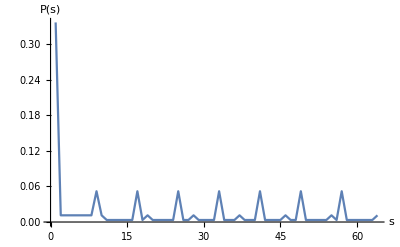

```mathematica
ListLinePlot[Table[Re[psynds[0.1,0.1,s]],{s,1,2^(nqubits-kqubits)}],AxesLabel->{"s","P(s)"},PlotRange->Full]
```

### Lookup table tailored to the physical noise map.

```mathematica
Recovery[Γ_,s_]:=Module[{probs},
probs = Table[Sum[Product[Γ[[1+LogicalAction[[u]][[i]][[q]]]][[1+LogicalAction[[u]][[j]][[q]]]],{q,1,nqubits}]*Phases[[u]][[i]]*Phases[[u]][[j]]*StabilizerSyndromeSigns[[s]][[j]]*Algebra[l-1,u-1],{i,1,2^(nqubits-kqubits)},{j,1,2^(nqubits-kqubits)},{u,1,4^kqubits}],{l,1,4}
];
Ordering[probs, -1][[1]]
];
```

```mathematica
lookup = Table[Recovery[process[0.05,0.1],s],{s,1,2^(nqubits-kqubits)}];
```

### The lookup table provides the logical Pauli correction to be applied for every syndrome measurement result.

```mathematica
Grid[Prepend[Table[{BaseForm[s-1,2],{"I","X̄","Ȳ","Z̄"}[[lookup[[s]]]]},{s,1,2^(nqubits-kqubits)}],{"s","L^⋆"}],Frame->All]//TableForm
```

s | L^⋆
0_2 | I
1_2 | X̄
10_2 | X̄
11_2 | X̄
100_2 | I
101_2 | I
110_2 | I
111_2 | I
1000_2 | Z̄
1001_2 | Ȳ
1010_2 | Ȳ
1011_2 | Ȳ
1100_2 | Z̄
1101_2 | Z̄
1110_2 | Z̄
1111_2 | Z̄
10000_2 | Z̄
10001_2 | Ȳ
10010_2 | Ȳ
10011_2 | Ȳ
10100_2 | Z̄
10101_2 | Z̄
10110_2 | Z̄
10111_2 | Z̄
11000_2 | Z̄
11001_2 | Ȳ
11010_2 | Ȳ
11011_2 | Ȳ
11100_2 | Z̄
11101_2 | Z̄
11110_2 | Z̄
11111_2 | Z̄
100000_2 | I
100001_2 | Ȳ
100010_2 | X̄
100011_2 | Ȳ
100100_2 | I
100101_2 | Z̄
100110_2 | Z̄
100111_2 | Z̄
101000_2 | I
101001_2 | Ȳ
101010_2 | Ȳ
101011_2 | Ȳ
101100_2 | Z̄
101101_2 | I
101110_2 | Z̄
101111_2 | Z̄
110000_2 | I
110001_2 | Ȳ
110010_2 | Ȳ
110011_2 | Ȳ
110100_2 | Z̄
110101_2 | Z̄
110110_2 | I
110111_2 | Z̄
111000_2 | I
111001_2 | Ȳ
111010_2 | Ȳ
111011_2 | Ȳ
111100_2 | Z̄
111101_2 | Z̄
111110_2 | Z̄
111111_2 | I

### Average effective channel.

```mathematica
Effective[Γ_,s_,a_,b_]:=Sum[Product[Γ[[1+LogicalAction[[a]][[i]][[q]]]][[1+LogicalAction[[b]][[j]][[q]]]],{q,1,nqubits}]*Phases[[a]][[i]]*Phases[[b]][[j]]*StabilizerSyndromeSigns[[s]][[j]],{i,1,2^(nqubits-kqubits)},{j,1,2^(nqubits-kqubits)}]*Algebra[lookup[[s]]-1,b-1]/(2^(nqubits-kqubits));
AverageLogical[Γ_]:=ParallelTable[Sum[Effective[Γ,s,i,j],{s,1,2^(nqubits-kqubits)}],{i,1,4^kqubits},{j,1,4^kqubits}];
```

```mathematica
logchan[p_,λ_]:= Refine[AverageLogical[process[p,λ]],Element[p,Reals]&&Element[λ,Reals]&&0≤p≤1&&0≤λ≤1];
```

```mathematica
logchan[p,λ]
```

{{7/32 (1+6 (1-2 p)^4 (1-λ)^2-(1-λ)^4-6 (1-2 p)^4 (1-λ)^4-λ^4)+21/32 (1-2 (1-2 p)^4 (1-λ)^2-(1-λ)^4+2 (1-2 p)^4 (1-λ)^4-λ^4)+7/64 (1-2 (1-2 p)^4 (1-λ)^2+7 (1-λ)^4-6 (1-2 p)^4 (1-λ)^4+7 λ^4)+1/64 (1+14 (1-2 p)^4 (1-λ)^2+7 (1-λ)^4+42 (1-2 p)^4 (1-λ)^4+7 λ^4),0,0,7/32 (λ^3-6 (1-2 p)^4 (1-λ)^2 λ^3-7 (1-λ)^4 λ^3-λ^7)+21/32 (λ^3+2 (1-2 p)^4 (1-λ)^2 λ^3-7 (1-λ)^4 λ^3-λ^7)+7/64 (7 λ^3-2 (1-2 p)^4 (1-λ)^2 λ^3+7 (1-λ)^4 λ^3+λ^7)+1/64 (7 λ^3+14 (1-2 p)^4 (1-λ)^2 λ^3+7 (1-λ)^4 λ^3+λ^7)},{0,7/64 ((1-2 p)^3 (1-λ)^(3/2)+6 (1-2 p)^3 (1-λ)^(7/2)-7 (1-2 p)^3 (1-λ)^(11/2)-7 (1-2 p)^3 (1-λ)^(3/2) λ^4)+7/64 (7 (1-2 p)^3 (1-λ)^(3/2)-6 (1-2 p)^3 (1-λ)^(7/2)-(1-2 p)^3 (1-λ)^(11/2)-(1-2 p)^3 (1-λ)^(3/2) λ^4)+23/64 (-(1-2 p)^3 (1-λ)^(3/2)+2 (1-2 p)^3 (1-λ)^(7/2)-(1-2 p)^3 (1-λ)^(11/2)-(1-2 p)^3 (1-λ)^(3/2) λ^4)+19/64 ((1-2 p)^3 (1-λ)^(3/2)-2 (1-2 p)^3 (1-λ)^(7/2)+(1-2 p)^3 (1-λ)^(11/2)+(1-2 p)^3 (1-λ)^(3/2) λ^4)+7/64 ((1-2 p)^3 (1-λ)^(3/2)+6 (1-2 p)^3 (1-λ)^(7/2)-8 (1-2 p)^7 (1-λ)^(7/2)+(1-2 p)^3 (1-λ)^(11/2)+(1-2 p)^3 (1-λ)^(3/2) λ^4)+1/64 (7 (1-2 p)^3 (1-λ)^(3/2)+42 (1-2 p)^3 (1-λ)^(7/2)+8 (1-2 p)^7 (1-λ)^(7/2)+7 (1-2 p)^3 (1-λ)^(11/2)+7 (1-2 p)^3 (1-λ)^(3/2) λ^4),0,0},{0,0,7/64 ((1-2 p)^3 (1-λ)^(3/2)+6 (1-2 p)^3 (1-λ)^(7/2)-7 (1-2 p)^3 (1-λ)^(11/2)-7 (1-2 p)^3 (1-λ)^(3/2) λ^4)+7/64 (7 (1-2 p)^3 (1-λ)^(3/2)-6 (1-2 p)^3 (1-λ)^(7/2)-(1-2 p)^3 (1-λ)^(11/2)-(1-2 p)^3 (1-λ)^(3/2) λ^4)+19/64 (-(1-2 p)^3 (1-λ)^(3/2)+2 (1-2 p)^3 (1-λ)^(7/2)-(1-2 p)^3 (1-λ)^(11/2)-(1-2 p)^3 (1-λ)^(3/2) λ^4)+23/64 ((1-2 p)^3 (1-λ)^(3/2)-2 (1-2 p)^3 (1-λ)^(7/2)+(1-2 p)^3 (1-λ)^(11/2)+(1-2 p)^3 (1-λ)^(3/2) λ^4)+7/64 ((1-2 p)^3 (1-λ)^(3/2)+6 (1-2 p)^3 (1-λ)^(7/2)-8 (1-2 p)^7 (1-λ)^(7/2)+(1-2 p)^3 (1-λ)^(11/2)+(1-2 p)^3 (1-λ)^(3/2) λ^4)+1/64 (7 (1-2 p)^3 (1-λ)^(3/2)+42 (1-2 p)^3 (1-λ)^(7/2)+8 (1-2 p)^7 (1-λ)^(7/2)+7 (1-2 p)^3 (1-λ)^(11/2)+7 (1-2 p)^3 (1-λ)^(3/2) λ^4),0},{0,0,0,7/32 ((1-λ)^3+6 (1-2 p)^4 (1-λ)^3-6 (1-2 p)^4 (1-λ)^5-(1-λ)^7-7 (1-λ)^3 λ^4)+21/32 ((1-λ)^3-2 (1-2 p)^4 (1-λ)^3+2 (1-2 p)^4 (1-λ)^5-(1-λ)^7-7 (1-λ)^3 λ^4)+7/64 (7 (1-λ)^3-6 (1-2 p)^4 (1-λ)^3-2 (1-2 p)^4 (1-λ)^5+(1-λ)^7+7 (1-λ)^3 λ^4)+1/64 (7 (1-λ)^3+42 (1-2 p)^4 (1-λ)^3+14 (1-2 p)^4 (1-λ)^5+(1-λ)^7+7 (1-λ)^3 λ^4)}}

```mathematica
MatrixForm[%75//FullSimplify]
```

(1 | 0 | 0 | -1/2 λ^3 (7+3 λ (-14+λ (21+2 λ (-7+2 λ))))
0 | 1/16 (-1+2 p)^3 (1-λ)^(3/2) (-16-96 p (-1+λ)^2+288 p^2 (-1+λ)^2-384 p^3 (-1+λ)^2+192 p^4 (-1+λ)^2+λ (-24+λ (58+23 (-2+λ) λ))) | 0 | 0
0 | 0 | 1/16 (-1+2 p)^3 (1-λ)^(3/2) (-16-96 p (-1+λ)^2+288 p^2 (-1+λ)^2-384 p^3 (-1+λ)^2+192 p^4 (-1+λ)^2+λ (-24+λ (50+19 (-2+λ) λ))) | 0
0 | 0 | 0 | 1/2 (-1+λ)^3 (-2+3 λ (-2+λ (3-2 λ+4 λ^2))))

### Logical error rate, i.e, the entanglement fidelity of the effective logical channel.

```mathematica
logInfid[p_,λ_]:=Refine[Infidelity[%75],Element[p,Reals]&&Element[λ,Reals]&&0≤p≤1&&0≤λ≤1];
```

```mathematica
Series[logInfid[p,λ],{p,0,2},{λ,0,2}]
```

((21 λ^2)/4+O[λ]^3)+((21 λ)/2-(231 λ^2)/8+O[λ]^3) p+(21-(189 λ)/2+(1197 λ^2)/8+O[λ]^3) p^2+O[p]^3

```mathematica
dephases=Table[N[(2/3)^i],{i,14,1,-1}];
relaxes=Table[N[(2/3)^i],{i,14,1,-1}];
```

```mathematica
logperf = Table[logInfid[p,λ],{p,dephases},{λ,relaxes}];
```

```mathematica
logperf
```

{{0.000422016,0.000556358,0.000812756,0.00131886,0.00234478,0.00446208,0.00886834,0.0180176,0.0367422,0.0739286,0.14405,0.265392,0.446383,0.647265},{0.000777211,0.00093935,0.00123693,0.00180367,0.00291801,0.00516238,0.00974707,0.0191379,0.03817,0.0757072,0.146145,0.2676,0.448242,0.648153},{0.00152056,0.00172274,0.00207964,0.00273368,0.00397527,0.00640233,0.0112432,0.0209801,0.0404511,0.078485,0.149361,0.270946,0.451034,0.649479},{0.00309099,0.00334964,0.00379015,0.00456718,0.00598789,0.00867178,0.0138721,0.0240926,0.0441731,0.0828878,0.154342,0.27604,0.455229,0.651452},{0.0064112,0.00674683,0.00730126,0.00824572,0.00990989,0.0129421,0.0186281,0.0294983,0.0503886,0.0899868,0.162142,0.28383,0.461529,0.654375},{0.0133682,0.0138032,0.0145044,0.0156643,0.0176409,0.0211184,0.0274214,0.0391078,0.0609948,0.101632,0.174491,0.295798,0.470975,0.658677},{0.0276423,0.0281937,0.0290667,0.0304779,0.0328173,0.0368076,0.0438119,0.0564053,0.0793512,0.120977,0.194202,0.31422,0.485066,0.664934},{0.0558457,0.0565103,0.0575495,0.0592019,0.0618853,0.0663524,0.0739868,0.0873443,0.111062,0.153109,0.225619,0.342409,0.505827,0.673857},{0.108176,0.108906,0.110039,0.111823,0.114682,0.119369,0.127235,0.140737,0.164251,0.20518,0.274574,0.384535,0.535571,0.686151},{0.195695,0.196376,0.19743,0.199087,0.201736,0.206063,0.213294,0.225642,0.247027,0.284011,0.346241,0.443859,0.575721,0.702049},{0.318308,0.318781,0.319521,0.320698,0.322611,0.325797,0.331243,0.34076,0.357599,0.387243,0.43773,0.517251,0.623587,0.72025},{0.441857,0.442043,0.442352,0.442878,0.443804,0.44549,0.44864,0.454627,0.466018,0.48726,0.524967,0.585805,0.667165,0.73633},{0.498837,0.498878,0.498967,0.499162,0.49959,0.500519,0.502522,0.50676,0.515482,0.532668,0.56431,0.616452,0.686426,0.743339},{0.532102,0.532057,0.532017,0.532018,0.532151,0.532636,0.533963,0.537173,0.544328,0.559136,0.587227,0.634288,0.697623,0.747407}}

```mathematica
Grid[Prepend[Table[Join[{dephases[[p]]},Table[logperf[[p]][[λ]],{λ,1,Length[relaxes]}]],{p,1,Length[dephases]}],Join[{"p"},Table[StringJoin["1-ℱ (λ = ", ToString[λ],")"],{λ,relaxes}]]],Frame->All]//TableForm
```

p | 1-ℱ (λ = 0.00342549) | 1-ℱ (λ = 0.00513823) | 1-ℱ (λ = 0.00770735) | 1-ℱ (λ = 0.011561) | 1-ℱ (λ = 0.0173415) | 1-ℱ (λ = 0.0260123) | 1-ℱ (λ = 0.0390184) | 1-ℱ (λ = 0.0585277) | 1-ℱ (λ = 0.0877915) | 1-ℱ (λ = 0.131687) | 1-ℱ (λ = 0.197531) | 1-ℱ (λ = 0.296296) | 1-ℱ (λ = 0.444444) | 1-ℱ (λ = 0.666667)
0.00342549 | 0.000422016 | 0.000556358 | 0.000812756 | 0.00131886 | 0.00234478 | 0.00446208 | 0.00886834 | 0.0180176 | 0.0367422 | 0.0739286 | 0.14405 | 0.265392 | 0.446383 | 0.647265
0.00513823 | 0.000777211 | 0.00093935 | 0.00123693 | 0.00180367 | 0.00291801 | 0.00516238 | 0.00974707 | 0.0191379 | 0.03817 | 0.0757072 | 0.146145 | 0.2676 | 0.448242 | 0.648153
0.00770735 | 0.00152056 | 0.00172274 | 0.00207964 | 0.00273368 | 0.00397527 | 0.00640233 | 0.0112432 | 0.0209801 | 0.0404511 | 0.078485 | 0.149361 | 0.270946 | 0.451034 | 0.649479
0.011561 | 0.00309099 | 0.00334964 | 0.00379015 | 0.00456718 | 0.00598789 | 0.00867178 | 0.0138721 | 0.0240926 | 0.0441731 | 0.0828878 | 0.154342 | 0.27604 | 0.455229 | 0.651452
0.0173415 | 0.0064112 | 0.00674683 | 0.00730126 | 0.00824572 | 0.00990989 | 0.0129421 | 0.0186281 | 0.0294983 | 0.0503886 | 0.0899868 | 0.162142 | 0.28383 | 0.461529 | 0.654375
0.0260123 | 0.0133682 | 0.0138032 | 0.0145044 | 0.0156643 | 0.0176409 | 0.0211184 | 0.0274214 | 0.0391078 | 0.0609948 | 0.101632 | 0.174491 | 0.295798 | 0.470975 | 0.658677
0.0390184 | 0.0276423 | 0.0281937 | 0.0290667 | 0.0304779 | 0.0328173 | 0.0368076 | 0.0438119 | 0.0564053 | 0.0793512 | 0.120977 | 0.194202 | 0.31422 | 0.485066 | 0.664934
0.0585277 | 0.0558457 | 0.0565103 | 0.0575495 | 0.0592019 | 0.0618853 | 0.0663524 | 0.0739868 | 0.0873443 | 0.111062 | 0.153109 | 0.225619 | 0.342409 | 0.505827 | 0.673857
0.0877915 | 0.108176 | 0.108906 | 0.110039 | 0.111823 | 0.114682 | 0.119369 | 0.127235 | 0.140737 | 0.164251 | 0.20518 | 0.274574 | 0.384535 | 0.535571 | 0.686151
0.131687 | 0.195695 | 0.196376 | 0.19743 | 0.199087 | 0.201736 | 0.206063 | 0.213294 | 0.225642 | 0.247027 | 0.284011 | 0.346241 | 0.443859 | 0.575721 | 0.702049
0.197531 | 0.318308 | 0.318781 | 0.319521 | 0.320698 | 0.322611 | 0.325797 | 0.331243 | 0.34076 | 0.357599 | 0.387243 | 0.43773 | 0.517251 | 0.623587 | 0.72025
0.296296 | 0.441857 | 0.442043 | 0.442352 | 0.442878 | 0.443804 | 0.44549 | 0.44864 | 0.454627 | 0.466018 | 0.48726 | 0.524967 | 0.585805 | 0.667165 | 0.73633
0.444444 | 0.498837 | 0.498878 | 0.498967 | 0.499162 | 0.49959 | 0.500519 | 0.502522 | 0.50676 | 0.515482 | 0.532668 | 0.56431 | 0.616452 | 0.686426 | 0.743339
0.666667 | 0.532102 | 0.532057 | 0.532017 | 0.532018 | 0.532151 | 0.532636 | 0.533963 | 0.537173 | 0.544328 | 0.559136 | 0.587227 | 0.634288 | 0.697623 | 0.747407

```mathematica
contourdata = ConstantArray[0,{Length[dephases]*Length[relaxes],3}];
point=1;
For[i=1,i≤Length[dephases],i++,
For[j=1,j≤Length[relaxes],j++,
contourdata[[point]][[1]]=dephases[[i]];
contourdata[[point]][[2]]=relaxes[[j]];
contourdata[[point]][[3]]=Log[logperf[[i]][[j]]];
point=point+1;
]
];
```

```mathematica
ListContourPlot[contourdata,ColorFunction->"TemperatureMap"]
```

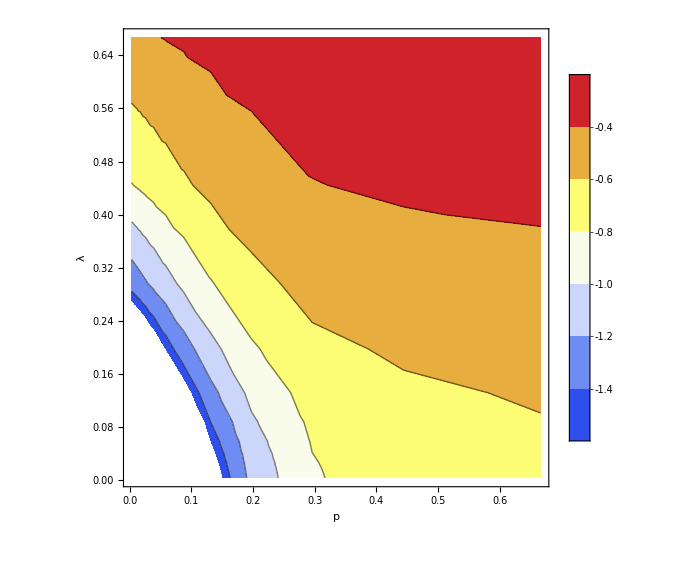

```mathematica
Show[ListContourPlot[contourdata,ColorFunction->"TemperatureMap",PlotLegends->Automatic],AxesLabel->{None,None},FrameLabel->{{HoldForm[λ],None},{HoldForm[p],None}},PlotLabel->None,LabelStyle->{FontFamily->"Helvetica",16,GrayLevel[0],Bold},ImageSize->Large]
```

## Plots comparing logical and physical noise rates.

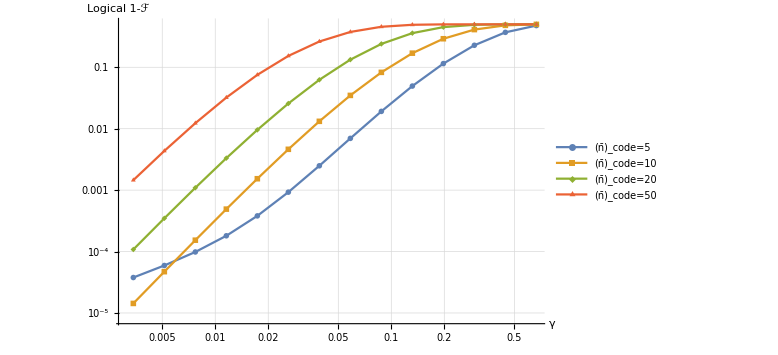

```mathematica
ListLogLogPlot[Table[Table[{physnoise[[i]],logperf7Rep[[i,j]]},{i,1,Length[physnoise]}],{j,1,Length[ncodes]}],AxesLabel->{"γ","Logical 1-ℱ"},PlotLegends->{"(n̄)_code=5","(n̄)_code=10","(n̄)_code=20","(n̄)_code=50"},Joined->True,PlotMarkers->{Automatic, Large},GridLines->Automatic,ImageSize->Large]
```

```mathematica
logperf7Rep
```

{{0.0000377588,0.0000143032,0.000108083,0.00145299},{0.0000592769,0.0000470156,0.000347661,0.00434728},{0.000098436,0.000153085,0.00109236,0.0122957},{0.000180577,0.000490488,0.00331582,0.0321188},{0.000380883,0.00153313,0.00957251,0.075252},{0.000926551,0.00461891,0.0257219,0.153054},{0.0024903,0.0131859,0.0625466,0.262657},{0.00695855,0.0348418,0.133129,0.375923},{0.0191381,0.0826408,0.240071,0.456233},{0.049454,0.169692,0.359521,0.491531},{0.114779,0.291357,0.450242,0.499389},{0.228078,0.410486,0.491347,0.499992},{0.370383,0.481379,0.49963,0.5},{0.477135,0.499384,0.5,0.5}}